{0.314159,0.628319,1.5708,2.82743}

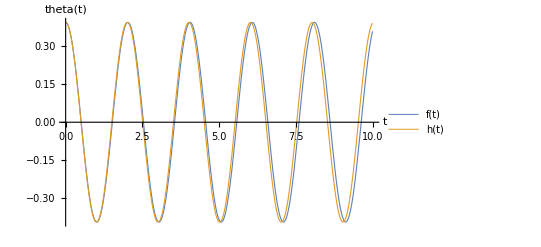

{-0.0522705}

2.02744

1.00972

```mathematica
(* Jai Prasadh *)
(* Based on code provided by Dr. Daniel Heinzen *)
(* Code for problem 1, HW2 *)

g:=9.792
l:=1.0
theta0:=0.125Pi
values = {0.1Pi, 0.2Pi, 0.5Pi, 0.9Pi}
fakeT = 2 Pi (l / g)^(0.5);

NDSolve[{theta''[t]+(g/l)Sin[theta[t]]==0,theta[0]==theta0,theta'[0]==0},theta,{t,0,10}];

f[t_]=theta[t]/.%;  (* f is exact solution *)

NDSolve[{theta''[t]+(g/l)theta[t]==0,theta[0]==theta0,theta'[0]==0},theta,{t,0,10}];

h[t_]=theta[t]/.%; (* h is SHM approximation sinTHETA = THETA *)

Plot[{f[t], h[t]},{t,0,10},AxesLabel->{"t","theta(t)"},PlotStyle->Thickness[0.002],AxesStyle->Directive[Thickness[0.002],14], PlotLegends->"Expressions"]

NIntegrate[f[t], {t, 0, 10}];
Print[%]

t1 = t /. FindRoot[f[t]==0,{t,1.5}];
t2 = t /. FindRoot[f[t]==0,{t,3.5}];
T = t2 - t1
(*Ratio of exact to approximate period  *)
Tratio = T / fakeT
```